```mathematica
f[x_]:=x^3
```

```mathematica
do[f[(i/j)*k],{i,1,10},{j,1,5},{k,1,2}]
```

do[(i^3 k^3)/j^3,{i,1,10},{j,1,5},{k,1,2}]

```mathematica
do[f[(i)],{i,1,10},{j,1,5},{k,1,2}]
```

do[i^3,{i,1,10},{j,1,5},{k,1,2}]

```mathematica
do[Print[f[(i)]],{i,1,10},{j,1,5},{k,1,2}]
```

i^3

do[Null,{i,1,10},{j,1,5},{k,1,2}]

```mathematica
i
```

i

```mathematica
f[i]
```

i^3

```mathematica
do[Print[f[2]],{i,1,10},{j,1,5},{k,1,2}]
```

8

do[Null,{i,1,10},{j,1,5},{k,1,2}]

```mathematica
do[Print[f[2]*i],{i,1,10},{j,1,5},{k,1,2}]
```

8 i

do[Null,{i,1,10},{j,1,5},{k,1,2}]

```mathematica
do[Print[i],{i,1,10},{j,1,5},{k,1,2}]
```

i

do[Null,{i,1,10},{j,1,5},{k,1,2}]

```mathematica
Do[Print[f[(i)]],{i,1,10},{j,1,5},{k,1,2}]
```

1

1

1

«7 more identical outputs»

8

8

8

«7 more identical outputs»

27

27

27

«7 more identical outputs»

64

64

64

«7 more identical outputs»

125

125

125

«7 more identical outputs»

216

216

216

«7 more identical outputs»

343

343

343

«7 more identical outputs»

512

512

512

«7 more identical outputs»

729

729

729

«7 more identical outputs»

1000

1000

1000

«7 more identical outputs»

```mathematica
do[Print[f[(i)]],{i,1,10},{j,1,5},{k,1,2}]
```

i^3

do[Null,{i,1,10},{j,1,5},{k,1,2}]

```mathematica
Do[Print[f[(i)]],{i,1,10},{j,1,5},{k,1,2}]
```

1

1

1

«7 more identical outputs»

8

8

8

«7 more identical outputs»

27

27

27

«7 more identical outputs»

64

64

64

«7 more identical outputs»

125

125

125

«7 more identical outputs»

216

216

216

«7 more identical outputs»

343

343

343

«7 more identical outputs»

512

512

512

«7 more identical outputs»

729

729

729

«7 more identical outputs»

1000

1000

1000

«7 more identical outputs»

```mathematica
1
```

1

```mathematica
PrimeQ[1]
```

False

```mathematica
7
```

7

```mathematica
N[First/@PowersRepresentations[PartitionsQ[7],2,2]]
```

{1.}

```mathematica
k
```

k

```mathematica
print
```

print

```mathematica
Print[k]
```

k

```mathematica
(x+1)^3
```

(1+x)^3

```mathematica
Expand[(x+1)^3]
```

1+3 x+3 x^2+x^3

```mathematica
x=x+1
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

Hold[1+x]

```mathematica
x=1
```

1

```mathematica
x*y=2
```

Set::write: Tag Times in 1\ y is Protected.

2

```mathematica
y
```

y

```mathematica
y/1
```

y

```mathematica
y/2
```

y/2

```mathematica
Variables[y]
```

{y}

```mathematica
y
```

y

```mathematica
x=y*2
```

2 y

```mathematica
x
```

2 y

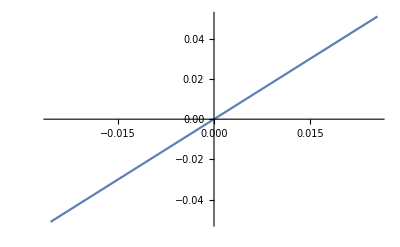

```mathematica
Plot[2 y,{y,-0.025500000000000002,0.025500000000000002}]
```

```mathematica
x=1=2y
```

Set::setraw: Cannot assign to raw object 1.

2 y

```mathematica
x==2y
```

True

```mathematica
x==1
```

2 y==1

```mathematica
Solve[x==1,{y}]
```

{{y→1/2}}

WolframAlphaQueryNoResults

WolframAlphaQueryParseResults

Stephen Wolfram

WolframAlphaQueryParseResults

Wolfram Research

WolframAlphaQueryNoResults

WolframAlphaQueryNoResults

WolframAlphaQueryResults

-Graphics-

WolframAlphaQueryParseResults

34.0147

WolframAlphaQueryParseResults

15.9994

WolframAlphaQueryParseResults

2.01588

WolframAlphaQueryParseResults

34.0147

WolframAlphaQueryResults

31.9988

```mathematica
f(x,y):=x*y
```

Syntax::sntxf: "(" cannot be followed by "x, y)""".

```mathematica
f[x_,y_]:=x+y
```

```mathematica
f[1,2]
```

3

```mathematica
Table[f[i,j],{i,2},{j,2}]
```

{{2,3},{3,4}}

```mathematica
MatrixForm[Table[f[i,j],{i,2},{j,2}]]
```

(2 | 3
3 | 4)

```mathematica
PrimeQ[PrimePi[Total[Sort[Reverse[First/@Table[f[i,j],{i,2,3},{j,2,3}]]]]]]
```

False

```mathematica
Needs["WSMLink`"]
```

```mathematica
fie=field[4,0]
```

WSMSimulate::bld: Failed to build model "EFieldLine.EFieldRunner".

WSMSimulate::bldl: "[/Users/Shanku/Documents/GitHub/EFieldLine/EFieldLine/Components/TParticle.mo:21:3-21:11:writable] Error: Type mismatch in equation tparticle1.E.Px=tparticle1.x of type Real(quantity = \\\"Length\\\", unit = \\\"m\\\")=Boolean."

WSMSimulate::bldl: "Error: Error occurred while flattening model EFieldLine.EFieldRunner"

$Failed

```mathematica
fie=field[4,0]
```

WSMSimulate::bld: Failed to build model "EFieldLine.EFieldRunner".

WSMSimulate::bldl: "[<interactive>:8:3-8:188:writable] Warning: Connecting two signal sources while connecting tparticle1.y to yField."

WSMSimulate::bldl: "[<interactive>:9:3-9:194:writable] Warning: Connecting two signal sources while connecting tparticle1.x to xField."

WSMSimulate::bldl: "Error: Simulation model is not globally balanced, having 23 variables and 25 equations."

General::stop: Further output of WSMSimulate :: bldl will be suppressed during this calculation.

$Failed

```mathematica
fie=field[4,0]
```

WSMSimulate::msg: "[terminate]: came close enough"

WSMSimulate::msg: "Simulation terminated at time 32.865"

WSMSimulate::term: Simulation of "EFieldLine.EFieldRunner" terminated because of a terminate statement.

WSMSimulationData[…]

```mathematica
ParametricPlot[{xField[x],yField[x]},{x,0,32.865}]
```

-Graphics-

```mathematica
xField=fie["tparticle1.x"]
```

InterpolatingFunction[{{0., 32.865}}, <>]

```mathematica
yField=fie["tparticle1.y"]
```

InterpolatingFunction[{{0., 32.865}}, <>]

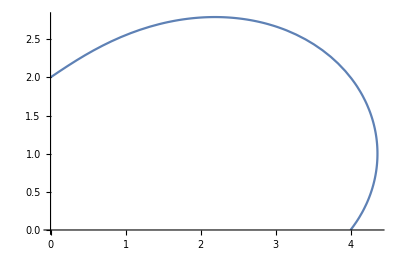

```mathematica
ParametricPlot[{xField[x],yField[x]},{x,0,32.865}]
```

```mathematica
fie2=field[4,1]
```

WSMSimulate::msg: "[terminate]: came close enough"

WSMSimulate::msg: "Simulation terminated at time 25.1148"

WSMSimulate::term: Simulation of "EFieldLine.EFieldRunner" terminated because of a terminate statement.

WSMSimulationData[…]

```mathematica
xField2=fie["tparticle1.x"]
```

InterpolatingFunction[{{0., 32.865}}, <>]

```mathematica
xField2=fie2["tparticle1.x"]
```

InterpolatingFunction[{{0., 25.1148}}, <>]

```mathematica
yField2=fie2["tparticle1.y"]
```

InterpolatingFunction[{{0., 25.1148}}, <>]

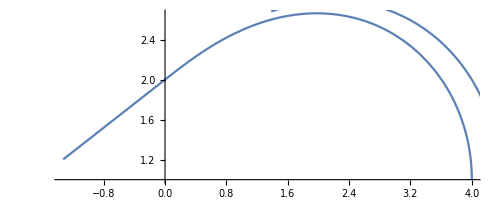

```mathematica
Show[ParametricPlot[{xField2[x],yField2[x]},{x,0,32.865}],ParametricPlot[{xField[x],yField[x]},{x,0,25.1148}]]
```

```mathematica
Show[%98,ImageSize->Tiny]
```

-Graphics-

```mathematica
pfie=ParametricPlot[{xField[x],yField[x]},{x,0,32.865}]
```

-Graphics-

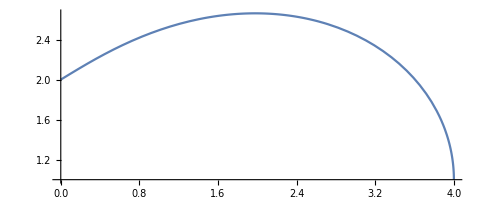

```mathematica
pfie2=ParametricPlot[{xField2[x],yField2[x]},{x,0,25.1148}]
```

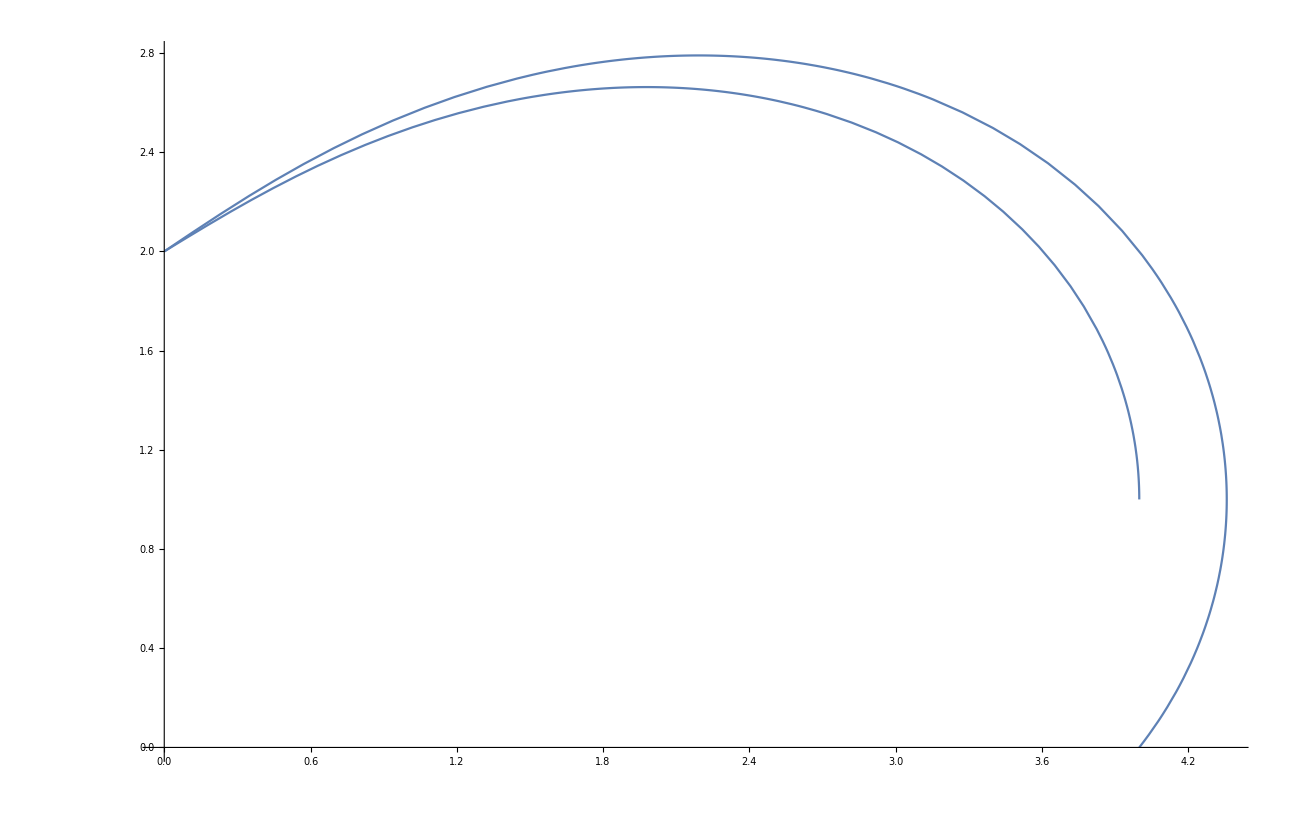

```mathematica
Show[pfie,pfie2]
```

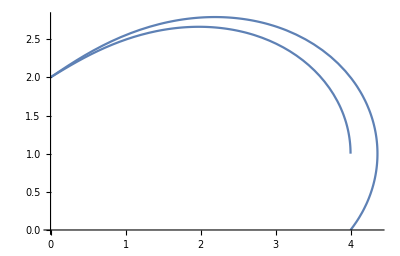

```mathematica
Show[%102,ImageSize->Full]
```

```mathematica
a[1,1]=1
```

1

```mathematica
a[1,2]=2
```

2

```mathematica
a
```

a

```mathematica
Information[a]
```

Global`a

a[1,1]=1
 
a[1,2]=2

```mathematica
a[1,:]
```

Syntax::tsntxi: "a[1, :]" is incomplete; more input is needed.""

```mathematica
xField
```

InterpolatingFunction[{{0., 32.865}}, <>]

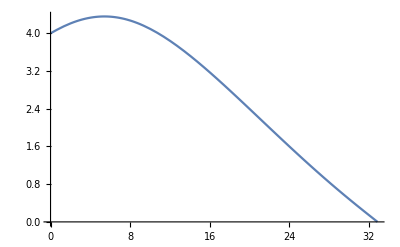

```mathematica
Plot[%108[x],{x,0.,32.86502620577364}]
```

```mathematica
Evaluate[xField]
```

InterpolatingFunction[{{0., 32.865}}, <>]

```mathematica
%110[1.23]
```

4.13903

```mathematica
ftest[x0_]:=
Module[{x=x0},
While[x>0,x=Log[x]];
x
]

ftest[2.0]
Evaluate(3+5)
```

-0.366513

8 Evaluate

```mathematica
ftest[1]
```

0

```mathematica
ftest[x0_, y0_]:= WSMSimulate["EfieldRunner", WSMParameterValues->{"tparticle1.x0"->{x0},"tparticle1.y0"->{y0}}]
```

```mathematica
f1 = ftest[4,1];
```

```mathematica
f1
```

WSMSimulate[EfieldRunner,WSMParameterValues→{tparticle1.x0→{4},tparticle1.y0→{1}}]

```mathematica
f1p =InterpolatingFunction[ f1];
```

```mathematica
f1p
```

InterpolatingFunction[WSMSimulate[EfieldRunner,WSMParameterValues→{tparticle1.x0→{4},tparticle1.y0→{1}}]]

```mathematica
f1=ftest[4,1]
```

WSMSimulate[EfieldRunner,WSMParameterValues→{tparticle1.x0→{4},tparticle1.y0→{1}}]

```mathematica
Needs["WSMLink`"]
```

WSMSimulate::shdw: Symbol "WSMSimulate" appears in multiple contexts {"WSMLink`", "Global`"}; definitions in context "WSMLink`" may shadow or be shadowed by other definitions.

WSMParameterValues::shdw: Symbol "WSMParameterValues" appears in multiple contexts {"WSMLink`", "Global`"}; definitions in context "WSMLink`" may shadow or be shadowed by other definitions.

```mathematica
Needs["WSMLink`"]
```

```mathematica
XY0={{4,1},{5,1}}
```

{{4,1},{5,1}}

```mathematica
Map[ftest,XY0]
```

{ftest[{4,1}],ftest[{5,1}]}

```mathematica
ftest[x0_, y0_]:= WSMSimulate["EfieldRunner", WSMParameterValues->{"tparticle1.x0"->{x0},"tparticle1.y0"->{y0}}]
```

```mathematica
fr1=Map[ftest,XY0]
```

{ftest[{4,1}],ftest[{5,1}]}

```mathematica
fr1 = ftest[5,1]
```

WSMLink::nomod: The class "EfieldRunner" was not found.

```mathematica
WSMSimulate["EfieldRunner",WSMParameterValues->{"tparticle1.x0"->{5},"tparticle1.y0"->{1}}]
```

WSMLink::nomod: The class "EfieldRunner" was not found.

```mathematica
WSMSimulate["EfieldRunner",WSMParameterValues->{"tparticle1.x0"->{5},"tparticle1.y0"->{1}}]
```

WSMLink::nomod: The class "EfieldRunner" was not found.

```mathematica
WSMSimulate["EfieldRunner",WSMParameterValues->{"tparticle1.x0"->{5},"tparticle1.y0"->{1}}]
Needs[WSMLinks]
```

WSMLink::nomod: The class "EfieldRunner" was not found.

```mathematica
WSMSimulate["EfieldRunner",WSMParameterValues->{"tparticle1.x0"->{5},"tparticle1.y0"->{1}}]
```

WSMLink::nomod: The class "EfieldRunner" was not found.

```mathematica
WSMSimulate["EfieldRunner",WSMParameterValues->{"tparticle1.x0"->{5},"tparticle1.y0"->{1}}]
```

WSMLink::nomod: The class "EfieldRunner" was not found.

WSMSimulate[EfieldRunner,WSMParameterValues→{tparticle1.x0→{5},tparticle1.y0→{1}}]

```mathematica
Needs["WSMLink`"]
```

```mathematica
ftest[x0_, y0_]:= WSMSimulate["EfieldRunner", WSMParameterValues->{"tparticle1.x0"->{x0},"tparticle1.y0"->{y0}}]
```

```mathematica
fr1=ftest[5,1]
```

WSMLink::nomod: The class "EfieldRunner" was not found.

WSMSimulate[EfieldRunner,WSMParameterValues→{tparticle1.x0→{5},tparticle1.y0→{1}}]

```mathematica
Needs["WSMLink`"]
```

```mathematica
fr1=ftest[5,1]
```

ftest[5,1]

```mathematica
ftest[{x0_, y0_}]:= WSMSimulate["EFieldRunner", WSMParameterValues->{"tparticle1.x0"->{x0},"tparticle1.y0"->{y0}}]
```

```mathematica
fr1=ftest[{5,1}]
```

WSMSimulate::msg: "[terminate]: came close enough"

WSMSimulate::msg: "Simulation terminated at time 31.6633"

WSMSimulate::term: Simulation of "EFieldLine.EFieldRunner" terminated because of a terminate statement.

WSMSimulationData[…]

```mathematica
XY0={{4,1},{5,1}}
```

```mathematica
{{4,1},{5,1}}
fr2=Map[ftest,XY0]
```

{{4,1},{5,1}}

WSMSimulate::msg: "[terminate]: came close enough"

WSMSimulate::msg: "Simulation terminated at time 25.1148"

WSMSimulate::term: Simulation of "EFieldLine.EFieldRunner" terminated because of a terminate statement.

WSMSimulate::msg: "[terminate]: came close enough"

General::stop: Further output of WSMSimulate :: msg will be suppressed during this calculation.

WSMSimulate::term: Simulation of "EFieldLine.EFieldRunner" terminated because of a terminate statement.

{WSMSimulationData[…],WSMSimulationData[…]}

```mathematica
fr2
```

{WSMSimulationData[…],WSMSimulationData[…]}

```mathematica
fr2[[1]]
```

WSMSimulationData[…]

```mathematica
XY0a=Table[{Cos[theta],Sin[theta]},{theta,0,2*Pi,2*Pi/10}]
```

{{1,0},{1/4 (1+√5),√(5/8-(√5)/8)},{1/4 (-1+√5),√(5/8+(√5)/8)},{1/4 (1-√5),√(5/8+(√5)/8)},{1/4 (-1-√5),√(5/8-(√5)/8)},{-1,0},{1/4 (-1-√5),-√(5/8-(√5)/8)},{1/4 (1-√5),-√(5/8+(√5)/8)},{1/4 (-1+√5),-√(5/8+(√5)/8)},{1/4 (1+√5),-√(5/8-(√5)/8)},{1,0}}

```mathematica
fra2=Map[ftest,XY0a]
```

WSMSimulate::msg: "[terminate]: came close enough"

WSMSimulate::msg: "Simulation terminated at time 20.3625"

WSMSimulate::term: Simulation of "EFieldLine.EFieldRunner" terminated because of a terminate statement.

WSMSimulate::msg: "[terminate]: came close enough"

General::stop: Further output of WSMSimulate :: msg will be suppressed during this calculation.

WSMSimulate::term: Simulation of "EFieldLine.EFieldRunner" terminated because of a terminate statement.

General::stop: Further output of WSMSimulate :: term will be suppressed during this calculation.

{WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…]}

```mathematica
createStartPoints[x0_,y0_,r_,n_]:=Table[{r*Cos[theta]+x0,r*Sin[theta]+y0},{theta,0,2*Pi,2*Pi/n}]
```

```mathematica
XY1 = createStartPoints[0,0,1,10]
```

{{1,0},{1/4 (1+√5),√(5/8-(√5)/8)},{1/4 (-1+√5),√(5/8+(√5)/8)},{1/4 (1-√5),√(5/8+(√5)/8)},{1/4 (-1-√5),√(5/8-(√5)/8)},{-1,0},{1/4 (-1-√5),-√(5/8-(√5)/8)},{1/4 (1-√5),-√(5/8+(√5)/8)},{1/4 (-1+√5),-√(5/8+(√5)/8)},{1/4 (1+√5),-√(5/8-(√5)/8)},{1,0}}

```mathematica
singleEfieldLineSim[{x0_, y0_}]:= WSMSimulate["EFieldRunner", WSMParameterValues->{"tparticle1.x0"->{x0},"tparticle1.y0"->{y0}}]
```

```mathematica
multipleEfieldLineSims[x0_,y0_,r_,n_]:=Map[singleEfieldLineSim,createStartPoints[x0,y0,r,n]]
```

```mathematica
mR1 = multipleEfieldLineSims[0,0,1,10]
```

WSMSimulate::msg: "[terminate]: came close enough"

WSMSimulate::msg: "Simulation terminated at time 20.3625"

WSMSimulate::term: Simulation of "EFieldLine.EFieldRunner" terminated because of a terminate statement.

WSMSimulate::msg: "[terminate]: came close enough"

General::stop: Further output of WSMSimulate :: msg will be suppressed during this calculation.

WSMSimulate::term: Simulation of "EFieldLine.EFieldRunner" terminated because of a terminate statement.

General::stop: Further output of WSMSimulate :: term will be suppressed during this calculation.

{WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…]}

```mathematica
mR1[[1]]
```

WSMSimulationData[…]

```mathematica
mR1x=mR1["tparticle1.x"]
```

{WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…]}[tparticle1.x]

```mathematica
mR1y=Table[mR1["tparticle1.y"],{1,Length[mR1[[i]]]}]
```

Table::itraw: Raw object 1 cannot be used as an iterator.

Table[mR1[tparticle1.y],{1,Length[mR1⟦i⟧]}]

```mathematica
ParametricPlot[{mR1x[[1]][x],mR1y[[1]][x]},{x,0,20}]
```

-Graphics-

```mathematica
x1=mR1[[1]]["tparticle1.x"]
y1=mR1[[1]]["tparticle1.y"]
```

InterpolatingFunction[{{0., 20.3625}}, <>]

InterpolatingFunction[{{0., 20.3625}}, <>]

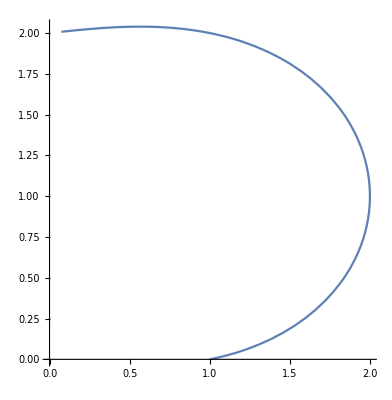

```mathematica
ParametricPlot[{x1[t],y1[t]},{t,0,20}]
```

```mathematica
mR1[[1]]["SimulationInterval"][[2]]
```

20.3625

```mathematica
yR1=Table[mR1[[i]]["tparticle1.y"],{i,1,10}]
```

{InterpolatingFunction[{{0., 20.3625}}, <>],InterpolatingFunction[{{0., 9.44835}}, <>],InterpolatingFunction[{{0., 5.51726}}, <>],InterpolatingFunction[{{0., 5.51726}}, <>],InterpolatingFunction[{{0., 9.44835}}, <>],InterpolatingFunction[{{0., 20.3625}}, <>],InterpolatingFunction[{{0., 63.1221}}, <>],InterpolatingFunction[{{0., 100.}}, <>],InterpolatingFunction[{{0., 100.}}, <>],InterpolatingFunction[{{0., 63.1221}}, <>]}

```mathematica
{InterpolatingFunction[{{0., 20.3625}}, <>],InterpolatingFunction[{{0., 9.44835}}, <>],InterpolatingFunction[{{0., 5.51726}}, <>],InterpolatingFunction[{{0., 5.51726}}, <>],InterpolatingFunction[{{0., 9.44835}}, <>],InterpolatingFunction[{{0., 20.3625}}, <>],InterpolatingFunction[{{0., 63.1221}}, <>],InterpolatingFunction[{{0., 100.}}, <>],InterpolatingFunction[{{0., 100.}}, <>],InterpolatingFunction[{{0., 63.1221}}, <>]}
xR1=Table[mR1[[i]]["tparticle1.x"],{i,1,10}]

ParametricPlot[{xR1[t],yR1[t]},{t,0,20}]
Length[mR1]
```

General::noinfo: Input expression InterpolatingFunction[{{0., 20.3625}}, <>] contains insufficient information to interpret the result.

```mathematica
Dimensions[mR1]
```

{11}

```mathematica
yR1=Table[mR1[[i]]["tparticle1.y"],{i,1,Dimensions[mR1][[1]]}]
```

{InterpolatingFunction[{{0., 20.3625}}, <>],InterpolatingFunction[{{0., 9.44835}}, <>],InterpolatingFunction[{{0., 5.51726}}, <>],InterpolatingFunction[{{0., 5.51726}}, <>],InterpolatingFunction[{{0., 9.44835}}, <>],InterpolatingFunction[{{0., 20.3625}}, <>],InterpolatingFunction[{{0., 63.1221}}, <>],InterpolatingFunction[{{0., 100.}}, <>],InterpolatingFunction[{{0., 100.}}, <>],InterpolatingFunction[{{0., 63.1221}}, <>],InterpolatingFunction[{{0., 20.3625}}, <>]}

```mathematica
xR1=Table[mR1[[i]]["tparticle1.x"],{i,1,Dimensions[mR1][[1]]}]
```

{InterpolatingFunction[{{0., 20.3625}}, <>],InterpolatingFunction[{{0., 9.44835}}, <>],InterpolatingFunction[{{0., 5.51726}}, <>],InterpolatingFunction[{{0., 5.51726}}, <>],InterpolatingFunction[{{0., 9.44835}}, <>],InterpolatingFunction[{{0., 20.3625}}, <>],InterpolatingFunction[{{0., 63.1221}}, <>],InterpolatingFunction[{{0., 100.}}, <>],InterpolatingFunction[{{0., 100.}}, <>],InterpolatingFunction[{{0., 63.1221}}, <>],InterpolatingFunction[{{0., 20.3625}}, <>]}

```mathematica
WSMModelData["EFieldLine.EFieldRunner"]
```

-Graphics-

```mathematica
dmR1=Dimensions[mR1][[1]]
```

11

```mathematica
EpPlot[1]
```

-Graphics-

```mathematica
dmR1SimTime[i_]:=mR1[[i]]["SimulationInterval"][[2]]
```

```mathematica
EpPlot[i_]:=ParametricPlot[{xR1[[i]][x],yR1[[i]][x]},{x,0,dmR1SimTime[i]}]
```

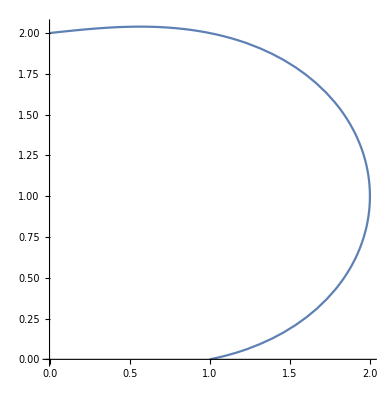

```mathematica
EpPlot[1]
```

```mathematica
ParametricPlot[{xR1⟦1⟧[x],yR1⟦1⟧[x]},{x,0,dmR1SimTime[1]}]
xR1
```

WSMSimulationData::urvs: The variables {"SimulationTime"} were not recognized.

WSMSimulationData::prop: Unknown property "SimulationTime".

Part::partw: Part 2 of … does not exist.

WSMSimulationData::urvs: The variables {"SimulationTime"} were not recognized.

WSMSimulationData::prop: Unknown property "SimulationTime".

Part::partw: Part 2 of … does not exist.

WSMSimulationData::urvs: The variables {"SimulationTime"} were not recognized.

General::stop: Further output of WSMSimulationData :: urvs will be suppressed during this calculation.

WSMSimulationData::prop: Unknown property "SimulationTime".

General::stop: Further output of WSMSimulationData :: prop will be suppressed during this calculation.

Part::partw: Part 2 of … does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ParametricPlot::plln: Limiting value … in {x, 0, dmR1SimTime[1]} is not a machine-sized real number.

ParametricPlot[{xR1⟦1⟧[x],yR1⟦1⟧[x]},{x,0,dmR1SimTime[1]}]

{InterpolatingFunction[{{0., 20.3625}}, <>],InterpolatingFunction[{{0., 9.44835}}, <>],InterpolatingFunction[{{0., 5.51726}}, <>],InterpolatingFunction[{{0., 5.51726}}, <>],InterpolatingFunction[{{0., 9.44835}}, <>],InterpolatingFunction[{{0., 20.3625}}, <>],InterpolatingFunction[{{0., 63.1221}}, <>],InterpolatingFunction[{{0., 100.}}, <>],InterpolatingFunction[{{0., 100.}}, <>],InterpolatingFunction[{{0., 63.1221}}, <>],InterpolatingFunction[{{0., 20.3625}}, <>]}

```mathematica
mR1
```

{WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…],WSMSimulationData[…]}

```mathematica
yR1=Table[mR1[[i]]["tparticle1.y"],{i,1,Dimensions[mR1][[1]]}]
```

{InterpolatingFunction[{{0., 20.3625}}, <>],InterpolatingFunction[{{0., 9.44835}}, <>],InterpolatingFunction[{{0., 5.51726}}, <>],InterpolatingFunction[{{0., 5.51726}}, <>],InterpolatingFunction[{{0., 9.44835}}, <>],InterpolatingFunction[{{0., 20.3625}}, <>],InterpolatingFunction[{{0., 63.1221}}, <>],InterpolatingFunction[{{0., 100.}}, <>],InterpolatingFunction[{{0., 100.}}, <>],InterpolatingFunction[{{0., 63.1221}}, <>],InterpolatingFunction[{{0., 20.3625}}, <>]}

```mathematica
xR1=Table[mR1[[i]]["tparticle1.x"],{i,1,Dimensions[mR1][[1]]}]
```

{InterpolatingFunction[{{0., 20.3625}}, <>],InterpolatingFunction[{{0., 9.44835}}, <>],InterpolatingFunction[{{0., 5.51726}}, <>],InterpolatingFunction[{{0., 5.51726}}, <>],InterpolatingFunction[{{0., 9.44835}}, <>],InterpolatingFunction[{{0., 20.3625}}, <>],InterpolatingFunction[{{0., 63.1221}}, <>],InterpolatingFunction[{{0., 100.}}, <>],InterpolatingFunction[{{0., 100.}}, <>],InterpolatingFunction[{{0., 63.1221}}, <>],InterpolatingFunction[{{0., 20.3625}}, <>]}

```mathematica
{InterpolatingFunction[{{0., 20.3625}}, <>],InterpolatingFunction[{{0., 9.44835}}, <>],InterpolatingFunction[{{0., 5.51726}}, <>],InterpolatingFunction[{{0., 5.51726}}, <>],InterpolatingFunction[{{0., 9.44835}}, <>],InterpolatingFunction[{{0., 20.3625}}, <>],InterpolatingFunction[{{0., 63.1221}}, <>],InterpolatingFunction[{{0., 100.}}, <>],InterpolatingFunction[{{0., 100.}}, <>],InterpolatingFunction[{{0., 63.1221}}, <>],InterpolatingFunction[{{0., 20.3625}}, <>]}
ParametricPlot[{xR1[[1]][t],yR1[[1]][t]},{t,0,20.1}]
```

General::noinfo: Input expression InterpolatingFunction[{{0., 20.3625}}, <>] contains insufficient information to interpret the result.

```mathematica
xR1[[1]]
```

InterpolatingFunction[{{0., 20.3625}}, <>]

```mathematica
x1 = xR1[[1]]
```

InterpolatingFunction[{{0., 20.3625}}, <>]

```mathematica
y1=yR1[[1]]
```

InterpolatingFunction[{{0., 20.3625}}, <>]

```mathematica
ParametricPlot[{x1[t],y1[t]},{t,0,20}]
```

```mathematica
-Graphics-
Range[x1]
```

-Graphics-

Range::range: Range specification in TagBox[InterpolatingFunction[{{0.`, 20.362548743512402`}}, {5, 7, 0, {309}, {2}, 0, 0, 0, 0, Automatic, {}, {}, False}, « 1 », {Developer`PackedArrayForm, {0, 1, « 47 », 49, « 260 »}, {1.`, 1.0129946838939177`, 1.0259701518352415`, 1.0389256254795263`, 1.051860251759862`, 1.0647731263137796`, 1.077663484861062`, 1.090530292049242`, 1.1033725366881983`, 1.1161891843262632`, 1.1289792031014465`, 1.1417415502866866`, « 28 », 1.4943030280234426`, 1.5056350311819366`, 1.5168952102889675`, 1.5280817267183104`, 1.539192714626857`, 1.5502262823713775`, 1.561180510059029`, 1.5720534529584682`, 1.5828431371695724`, 1.5935475665245042`, « 259 »}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]] does not have appropriate bounds.

Range[InterpolatingFunction[{{0., 20.3625}}, <>]]

```mathematica
x1[Domain]
```

{{0.,20.3625}}

```mathematica
∫%99ⅆData
```

InterpolatingFunction[{{0., 20.3625}}, <>][Data]

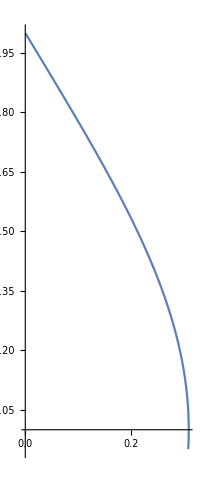
show[-Graphics-,-Graphics-]

```mathematica
show[%,EpPlot[3]]
```

```mathematica
p1=EpPlot[1]
```

-Graphics-

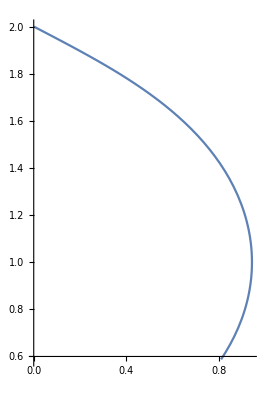

```mathematica
p2=EpPlot[2]
```

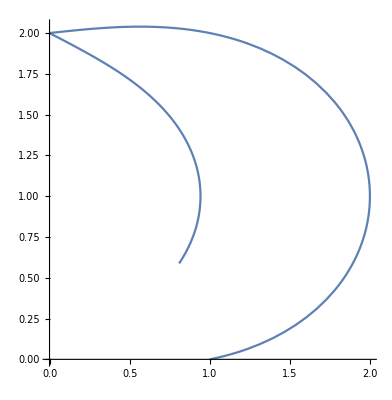

```mathematica
Show[p1,p2]
```

```mathematica
p={p1,p2}
```

{-Graphics-,-Graphics-}

```mathematica
show=.
```

```mathematica
Show[p]
```

-Graphics-

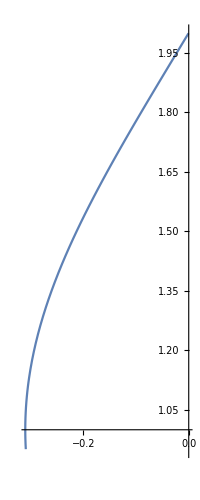
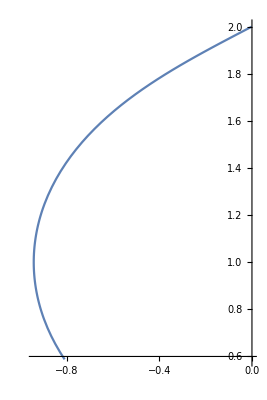
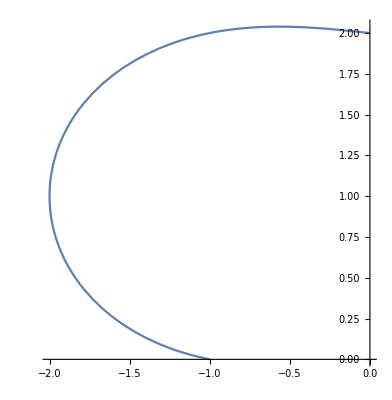
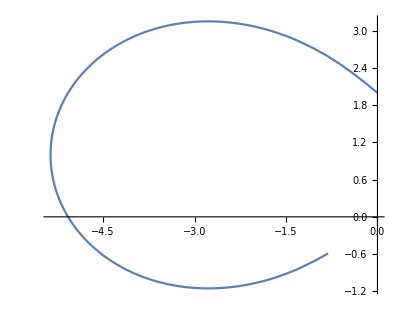
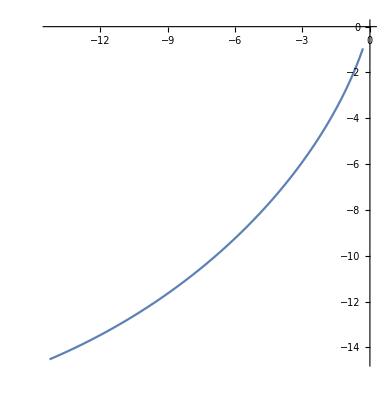
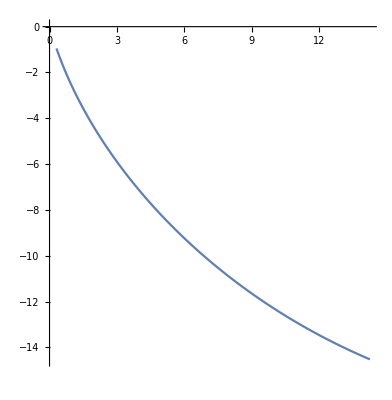
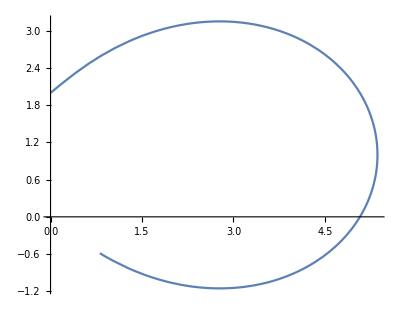
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
results=Table[EpPlot[i],{i,1,dmR1}]
```

```mathematica
show[results]
```

show[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]

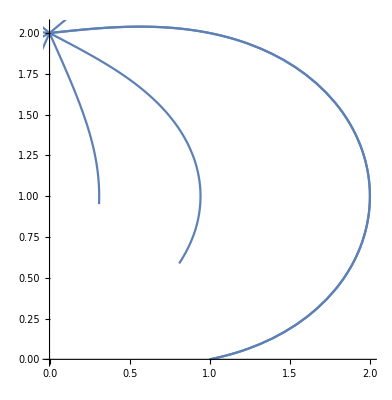

```mathematica
Show[results]
```

```mathematica
Show[%117,ImageSize->Full]
```

-Graphics-

```mathematica
Rasterize[%117,"Image"]
```

-Graphics-

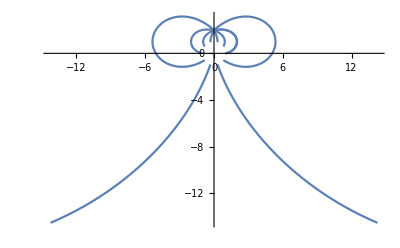

```mathematica
Show[results,PlotRange->All]
```